```mathematica
fA=Interpolation[{{505,4.604},{428.297,4.38197},
{361.351,3.66544},{258.657,2.46806},{176.763,1.65192},{113.067,1.09189},{54.5705,0.699649},{20.57384,0.523615}}];
fB={{519.6,0.5186},{521.2,0.5516},{530.4,0.7012},{538,0.9048},{544,1.15},{550,1.398},{554.8,1.707},{559.8,2.096},{563,2.56},{564,3.08}};
fC={{564,3.08},{563.5,3.36},{560.2,3.589},{555,3.819},{544,4.063},{534.6,4.263},{520.6,4.437},{505,4.604}};
```

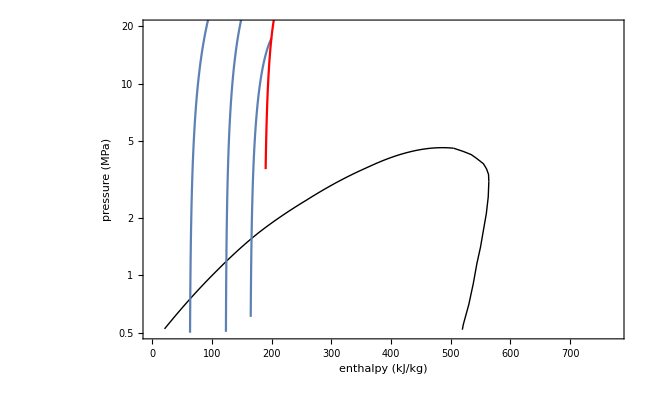

```mathematica
Module[{f1,g1,f2,g2,f3,h},

f1[x_]=-0.001*x^2+0.855*x-49.638;
f2[x_]=-0.0037*x^2+1.8417*x-169.41;
f3[x_]=-0.0268*x^2+11.864*x-1283.1;

h[x_]=-(0.001+i*0.0027)*x^2+(0.855+0.98*i)*x-(49.638+120*i);

Show[
ListLogPlot[{fB,fC},Joined->True,PlotStyle->{{Thick,Black}}],
LogPlot[fA[x],{x,20.57384,505},PlotStyle->{Thick,Black}],

Table[LogPlot[h[x],{x,50*(1+i),100+50*i}],{i,0,4}],
LogPlot[f3[x],{x,190,209},PlotStyle->Red],

Frame->True,FrameLabel->{Style["enthalpy (kJ/kg)",17],Style["pressure  (MPa)",17]},LabelStyle->{Black,14},
PlotRange->{{0,775},{Log@0.5,Log@20}},Axes->False,ImageSize->650]
]
```

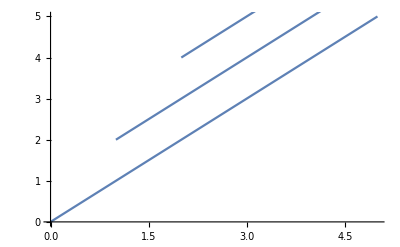

```mathematica
Show[Table[Plot[x+i,{x,i,i+5}],{i,0,3}]]
```

```mathematica
Module[{k},
k[x_]=x+j;
Show[Table[Plot[k[x],{x,j,j+5}],{j,0,3}]]
]
```

-Graphics-

```mathematica
Table[-(0.001+i*0.27)*x^2+(0.855+0.98*i)*x-(49.638+120*i),{i,0,3}]
```

{-49.638+0.855 x-0.001 x^2,-169.638+1.835 x-0.271 x^2,-289.638+2.815 x-0.541 x^2,-409.638+3.795 x-0.811 x^2}